```mathematica
rate[s_List]:=Block[{x,y,z,n=Length[s],t},
x=ConstantArray[1.0,n];
Reap[Do[
y=z=ConstantArray[0.0,n];
Do[
t=s⟦i,j⟧/(x⟦i⟧+x⟦j⟧);
print["t: ",t,"  x[i]: ",x⟦i⟧,"  x[j]: ",x⟦j⟧];
y⟦i⟧+=t*x⟦j⟧;z⟦j⟧+=t;
,{i,1,n},{j,1,n}];
x=y/z;
Print["x: ",x,"  y: ",y,"  z: ",z];
Sow[Log10[400]Log[x/Min[x]]];
,{20}]][[2,1]]//Transpose//ListPlot//Print;
Log[x/Min[x]] Log10[400]
]
```

x: {1.33333,0.75}  y: {2.,1.5}  z: {1.5,2.}

x: {1.18352,0.844937}  y: {1.58,1.78}  z: {1.335,2.10667}

x: {1.24224,0.804995}  y: {1.74962,1.66692}  z: {1.40844,2.07072}

x: {1.21763,0.821266}  y: {1.67963,1.71358}  z: {1.37942,2.08651}

x: {1.22769,0.814539}  y: {1.7084,1.6944}  z: {1.39155,2.0802}

x: {1.22354,0.817304}  y: {1.69654,1.7023}  z: {1.38659,2.08283}

x: {1.22524,0.816164}  y: {1.70142,1.69905}  z: {1.38864,2.08175}

x: {1.22454,0.816633}  y: {1.69941,1.70039}  z: {1.3878,2.0822}

x: {1.22483,0.81644}  y: {1.70024,1.69984}  z: {1.38815,2.08201}

x: {1.22471,0.81652}  y: {1.6999,1.70007}  z: {1.388,2.08209}

x: {1.22476,0.816487}  y: {1.70004,1.69997}  z: {1.38806,2.08206}

x: {1.22474,0.816501}  y: {1.69998,1.70001}  z: {1.38804,2.08207}

x: {1.22475,0.816495}  y: {1.70001,1.7}  z: {1.38805,2.08206}

x: {1.22474,0.816497}  y: {1.7,1.7}  z: {1.38804,2.08207}

x: {1.22475,0.816496}  y: {1.7,1.7}  z: {1.38804,2.08207}

x: {1.22474,0.816497}  y: {1.7,1.7}  z: {1.38804,2.08207}

x: {1.22474,0.816497}  y: {1.7,1.7}  z: {1.38804,2.08207}

x: {1.22474,0.816497}  y: {1.7,1.7}  z: {1.38804,2.08207}

«2 more identical outputs»

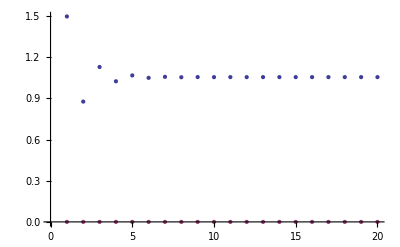

{1.05504,0.}

```mathematica
rate[({{1, 3}, {2, 1}})]
```

```mathematica
Table[Table[Floor[4.18Log[1+Log[i]]],{i,2,n}],{n,2,32}]//TableForm
```

```mathematica
3Log[2]//N
```

2.07944

```mathematica
Log[1+Log[i]]
```

```mathematica
Series[1]
```

```mathematica
Plot[Sqrt[10/(x^2+10)],{x,0,10},PlotRange->{0,1}]
```

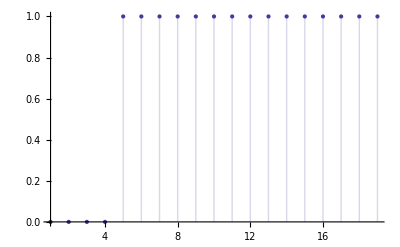

```mathematica
Table[With[{max=2},DiscretePlot[Floor[max (i/n)^(1/2)],{i,1,n-1}]],{n,{20}}]
```

```mathematica
(3Log[n])/((2+d/20)/3)//Together
```

(180 Log[n])/(40+d)

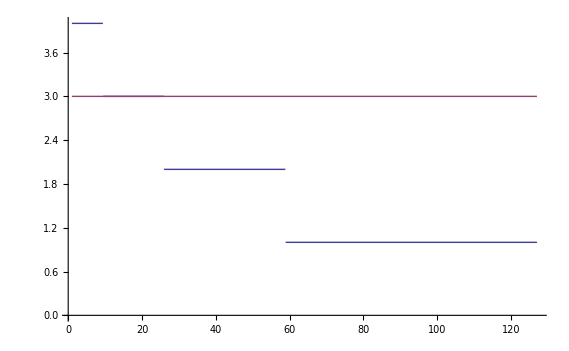

```mathematica
With[{n=3},Plot[{Floor[(3Log[n])/((2+d/20)/3)],Floor[3Log[n]]},{d,1,127},PlotRange->{0,Automatic}]]
```